```mathematica
eqn={
a1==ri1*iin1,
a2*iin2==ri2*iout,
Ig1*pin1==rp1*pout,
a2*iin2==Ig2*pin2-rp2*(pout-pin2),
x1*iin1==x2*iout,
x2*(pin2-pout)==x1*pout,
Ig1*y1*pin1*c1*(1-((x1+x2)/p))==d1,
Ig2*y2*pin2*c2*(1-((x1+x2)/p))==d2};
var={iin1,iin2,iout,pin1,pin2,pout,x1,x2};
para={y1,y2,c1,c2,d1,d2,Ig1,Ig2,a1,a2,ri1,ri2,rp1,rp2,p};
cond=ToExpression@Table[ToString@var[[i]]<>">0",{i,Length@var}];
eqn1=Join[eqn,cond]
```

{a1==iin1 ri1,a2 iin2==iout ri2,Ig1 pin1==pout rp1,a2 iin2==Ig2 pin2-(-pin2+pout) rp2,iin1 x1==iout x2,(pin2-pout) x2==pout x1,c1 Ig1 pin1 (1-(x1+x2)/p) y1==d1,c2 Ig2 pin2 (1-(x1+x2)/p) y2==d2,iin1>0,iin2>0,iout>0,pin1>0,pin2>0,pout>0,x1>0,x2>0}

```mathematica
result=Solve[eqn,var];
solve=var/.result;
nzsolve=solve[[2]];
simpsolve=Table[FullSimplify[nzsolve[[i]],{y1>0,y2>0,c1>0,c2>0,d1>0,d2>0,Ig1>0,Ig2>0,a1>0,a2>0,ri1>0,ri2>0,rp1>0,rp2>0,p>0}],{i,Length@var}];
reducesolve=Join[simpsolve,para];
solvecond=FullSimplify@Reduce[reducesolve>0,para]
```

y1>0&&y2>0&&c1>0&&c2>0&&d1>0&&d2>0&&Ig1>0&&Ig2>0&&a1>0&&a2>0&&ri1>0&&ri2>0&&a1 c1 d2 ri2 y1 (a1 c1 d2 ri2 rp1 y1-d1 Ig2 (d2 ri1+a1 c2 ri2 y2))>0&&0<rp2<c1 rp1 y1 ((a1 ri2)/(d1 ri1)+(d2 Ig2)/(-c1 d2 rp1 y1+c2 d1 Ig2 y2))&&p>0

```mathematica
Reduce[{d1 ri1 (Ig2-rp2)<a1 c1 ri2 rp1 y1,d1>0,Ig2>0,rp1>0,rp2>0,ri1>0,ri2>0,a1>0,c1>0,y1>0,rp2<Ig2},a1]
```

rp2>0&&Ig2>rp2&&y1>0&&rp1>0&&ri2>0&&ri1>0&&d1>0&&c1>0&&a1>(d1 Ig2 ri1-d1 ri1 rp2)/(c1 ri2 rp1 y1)

```mathematica
simpsolve[[-3]]
simpsolve[[-4]]
Simplify[(a1 c1 d2 ri2 rp1 y1)/(c2 d1 Ig2^2 ri1 y2-c2 d1 Ig2 ri1 rp2 y2)>(a1 ri2)/(Ig2 ri1-ri1 rp2),{d1 ri1 (Ig2-rp2)<a1 c1 ri2 rp1 y1,d1>0,Ig2>0,rp1>0,rp2>0,ri1>0,ri2>0,a1>0,c1>0,c2>0,y1>0,rp2<Ig2}]
c2 d1 Ig2 y2<c1 d2 rp1 y1
```

(a1 ri2)/(Ig2 ri1-ri1 rp2)

(a1 c1 d2 ri2 rp1 y1)/(c2 d1 Ig2^2 ri1 y2-c2 d1 Ig2 ri1 rp2 y2)

c2^2 d1 Ig2 y2^2<c1 c2 d2 rp1 y1 y2

c2 d1 Ig2 y2<c1 d2 rp1 y1

```mathematica
solvex1=simpsolve[[-2]];
solvex2=simpsolve[[-1]];
ratiox1=solvex1/(solvex1+solvex2);
ratiox2=solvex2/(solvex1+solvex2);
FullSimplify@ratiox1
FullSimplify@ratiox2
```

1-(c2 d1 Ig2 y2)/(c1 d2 rp1 y1)

(c2 d1 Ig2 y2)/(c1 d2 rp1 y1)

```mathematica
(c2 d1 Ig1 Ig2 y2)/(c1 d2 Ig1 rp y1-c2 d1 Ig2 rp y2)
m1=(c1 d2 Ig1 y1)/(c2 d1 Ig2 y2);
m2=Ig1/rp;
m2/(m1-1);
```

```mathematica
Manipulate[Plot3D[100*(m3)*(10^m2)/((10^m1)-(10^m2))&&m1>m2,{m1,-8,2},{m2,-8,2}],{m3,0,1}];
```

```mathematica
Plot3D[100*m2/(m1-1)&&m1>1,{m1,1,100},{m2,0,100},PlotRange->{0,100},RegionFunction->Function[{m1,m2},m1>1&&m2/(m1-1)<1]]
```

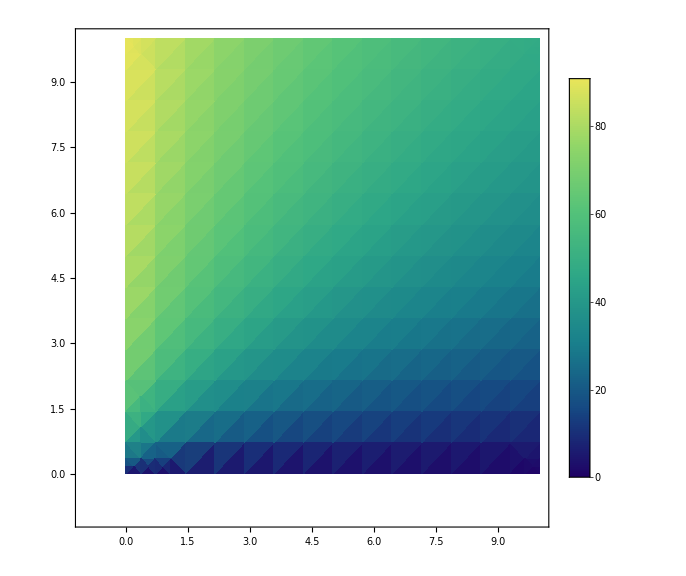

Export::nodir: Directory D:\Reasearch\reasearch\Model\newmodel5\2-member\additional\plot\ does not exist.

Export::noopen: Cannot open D:\Reasearch\reasearch\Model\newmodel5\2-member\additional\plot\deplot.tif.

```mathematica
deplot=DensityPlot[100*m2/(m1+m2+1),{m1,0,10},{m2,0,10},ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,LabelStyle->Directive[Black,Bold,20],PlotRange->{{-1,10},{-1,10},{0,100}},Frame->True,FrameStyle->Directive[Thickness[0.005],Black,Bold,24],ImageSize->Large]
Export[FileNameJoin[{NotebookDirectory[],"plot","deplot.tif"}],deplot];
```